```mathematica
Solve[{
a+b+c+d+e == 0,
-2a-b+d+2e==1,
2a+b/2+d/2+2e==0,
-4/3a-1/6b+1/6d+4/3e==0,
2/3a+1/24b+1/24d+2/3e==0
},{a,b,c,d,e}]
```

{{a→1/12,b→-2/3,c→0,d→2/3,e→-1/12}}

```mathematica
SetDirectory[NotebookDirectory[]];
```

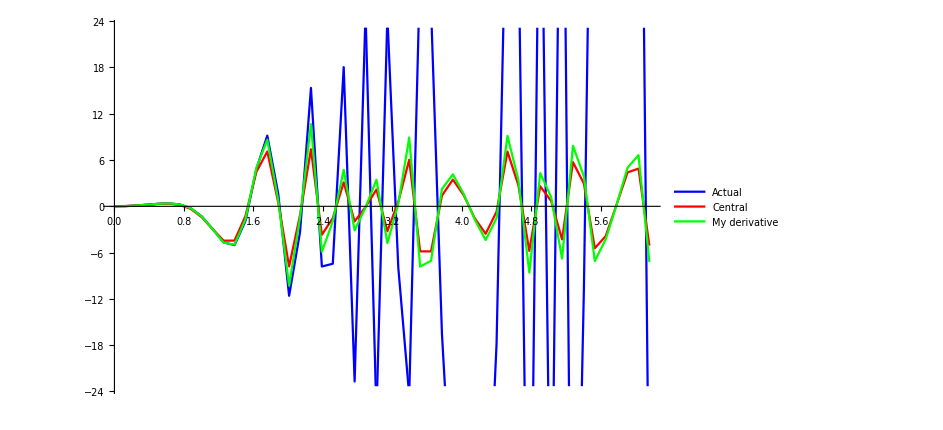
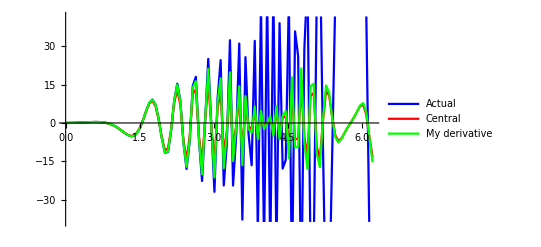
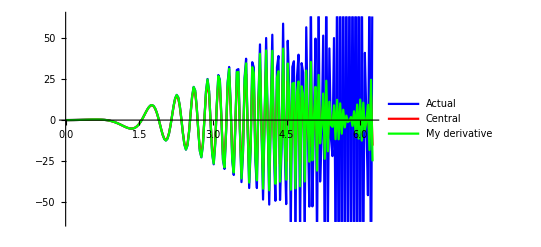
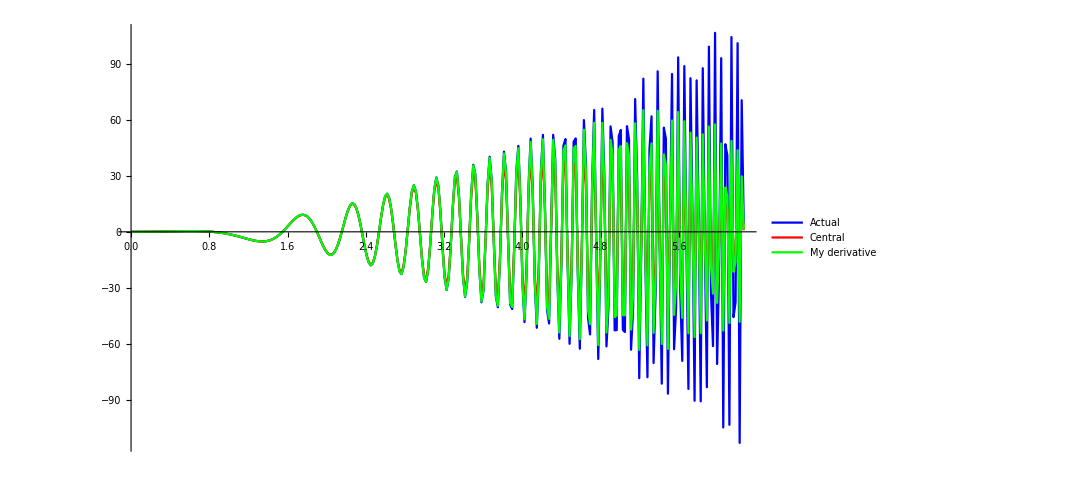
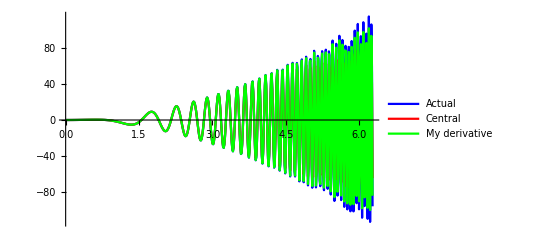

```mathematica
data = Import["outputs/uloha1_50.csv", "CSV"];
n50plot = ListLinePlot[{data[[All,{1,2}]],data[[All,{1,3}]],data[[All,{1,4}]]},PlotStyle->{Blue,Red, Green},PlotLegends->{"Actual", "Central","My derivative"},FrameLabel->{"x","f(x)"}];
data = Import["outputs/uloha1_100.csv", "CSV"];
n100plot = ListLinePlot[{data[[All,{1,2}]],data[[All,{1,3}]],data[[All,{1,4}]]},PlotStyle->{Blue,Red, Green},PlotLegends->{"Actual", "Central","My derivative"},FrameLabel->{"x","f(x)"}];
data = Import["outputs/uloha1_200.csv", "CSV"];
n200plot = ListLinePlot[{data[[All,{1,2}]],data[[All,{1,3}]],data[[All,{1,4}]]},PlotStyle->{Blue,Red, Green},PlotLegends->{"Actual", "Central","My derivative"},FrameLabel->{"x","f(x)"}];
data = Import["outputs/uloha1_300.csv", "CSV"];
n300plot = ListLinePlot[{data[[All,{1,2}]],data[[All,{1,3}]],data[[All,{1,4}]]},PlotStyle->{Blue,Red, Green},PlotLegends->{"Actual", "Central","My derivative"},FrameLabel->{"x","f(x)"}];
data = Import["outputs/uloha1_500.csv", "CSV"];
n500plot = ListLinePlot[{data[[All,{1,2}]],data[[All,{1,3}]],data[[All,{1,4}]]},PlotStyle->{Blue,Red, Green},PlotLegends->{"Actual", "Central","My derivative"},FrameLabel->{"x","f(x)"}];
{n50plot,n100plot,n200plot,n300plot, n500plot}
```

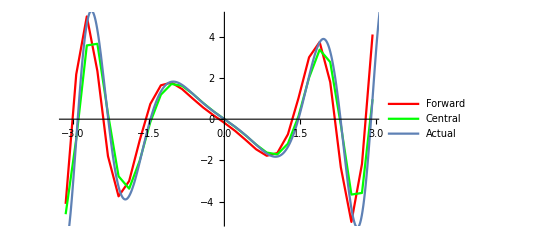

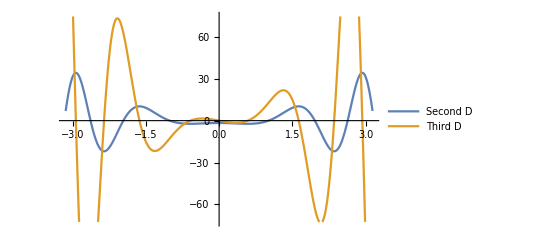

```mathematica
data = Import["outputs/uloha2.csv", "CSV"];
f[x_]:=Cos[x*x+1];
Show[ListLinePlot[{data[[All,{1,2}]], data[[All,{1,3}]]},PlotStyle->{Red, Green},PlotLegends->{"Forward", "Central"},FrameLabel->{"x","f'(x)"}],
Plot[f'[x],{x,-π, π}, PlotLegends->{"Actual"}]]
Plot[{f''[x], f'''[x]}, {x,-π, π},PlotLegends->{"Second D", "Third D"}]
```

```mathematica
Integrate[x^2, {x, -π, π}]//N
Integrate[Cos[x], {x, -π, π}]//N
```

20.6709

0.